## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

Dynamics of intermediate hosts

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - η Is ;  (*Susceptible host*)
dIwdt =  (1-p)η Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw;  (* Host infected with one parasite*)
dIwwdt =  p η Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; (* Host infected with two parasites*)
```

Dynamics of definitive hosts

```mathematica
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds; (*Susceptible host*)
dDwdt =(λw + (1-q)λww) Ds- (μ + σw) Dw - ((1-q)λww +λw)Dw; (*Host infected with one parasite*)
dDwwdt =  q λww Ds + ((1-q)λww + λw)Dw - (μ + σww)Dww; (* Host infected with two parasites*)
```

Dynamics of free-living parasites

```mathematica
dWdt = fw Dw +fww Dww- δ W - η Is;
```

Setting force of infection, and list of parameters for solving the odes

```mathematica
forceInf = {η -> γ W, λw ->h(ρ +  βw) Iw, λww ->h(ρ + βww) Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

Testing that the total dynamics of definitive host does not involve transmission

```mathematica
dDsdt + dDwdt + dDwwdt//FullSimplify
```

-Ds μ-Dw (μ+σw)-Dww (μ+σww)+B[Ds,Dw,Dww,Is,Iw,Iww]

# Reproduction ratio R0

This is the result from the file trophicaltransmission_analytical_git.nb

```mathematica
R0 = γ Is(p q h(βww + ρ))/(αww+d+ Πww[Ds, Dw, Dww,βww])  Ds/(μ+σww) fww/(δ+γ Is) +
γ Is (((1-p)(βw + ρ)h)/(αw+d+ Πw[Ds, Dw,Dww, βw]) + (p (1-q)(βww + ρ)h)/(αww+d+ Πww[Ds, Dw, Dww,βww]))  Ds/(μ+ σw)fw/(δ+γ Is);
```

# Graph format and parallel computation

```mathematica
includeFrame = True;
imageSize = 600;
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colorlist = ColorData[97,"ColorList"]
colorstable = ColorData[97,"ColorList"][[{1, 2, -2}]]
ihostCol = ColorData[97,"ColorList"][[1]];
 dhostCol = ColorData[97,"ColorList"][[4]];
fCol1 = ColorData[97,"ColorList"][[3]];
fCol2 = ColorData[97,"ColorList"][[-1]];
pointsize = 0.02;
figResolution = 300;
colbifur = {Black, Black, Black, Black};
colbifurfilling = {Lighter[Gray, 0.1],Lighter[Gray, 0.3], Lighter[Gray, 0.5], Lighter[Gray, 0.7]}
panellabel = 250;
thick = 0.003;
coldat = "Pastel";
intorder = 5;
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.736782672705901, 0.358, 0.5030266573755369]}

{RGBColor[0.55, 0.55, 0.55],RGBColor[0.65, 0.65, 0.65],RGBColor[0.75, 0.75, 0.75],RGBColor[0.85, 0.85, 0.85]}

# Linear birth function for intermediate host

Setting birth function

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

Solving the odes with linear birth function

```mathematica
solsds = Solve[Thread[sysfunc0 == 0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0}, varRes][[2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{Is→μ/(c ρ),Ds→-(d-r)/ρ}

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories (supplementary figure)

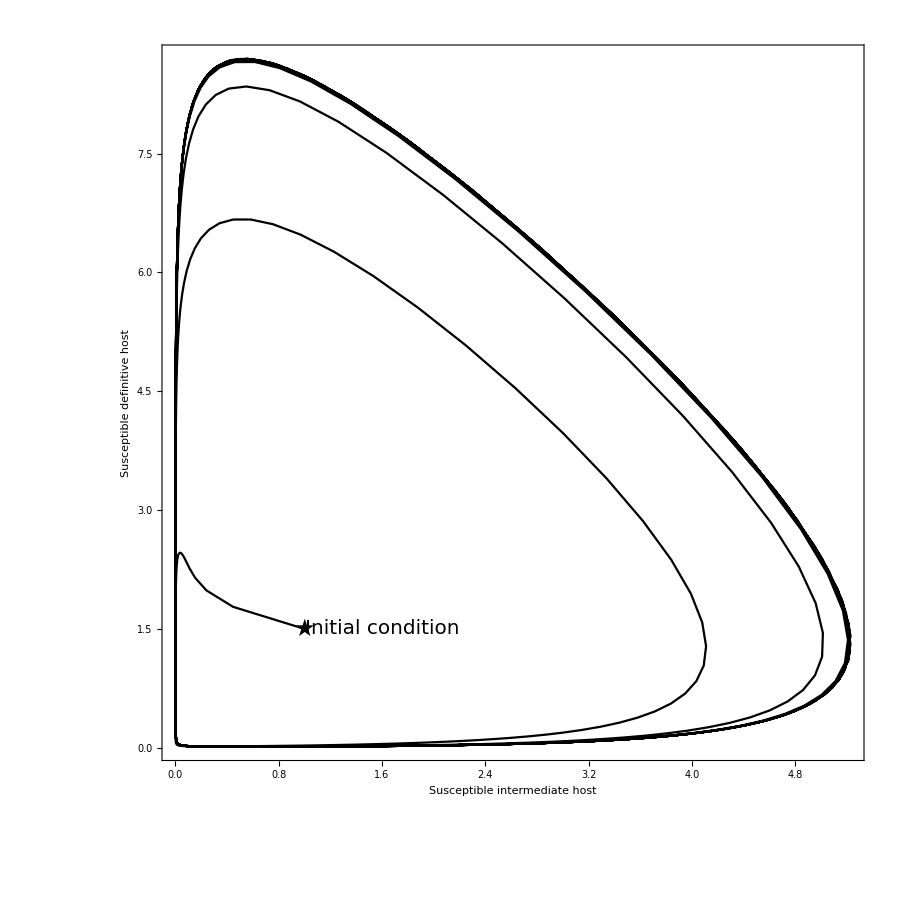

```mathematica
(*Set parameters*)prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9, h-> 0.8};
maxt = 100;

(*Set initial conditions for population dynamics*)
init0= {Is[0]== 1, Iw[0] == 1,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

(*Solving the equilibrium*)
sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
(*Solving the dynamics of the odes*)
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

(*Set the range for the graph*)
range = {{-1, 20},{-1, 20}};

(* Annotattion for the different lines*)
epilogParasite01 = { {Black, Line[{{8.5, 0.03}, {10.1, 0.81}}]},{Black, Line[{{7.5, 0.23}, {5.1, 0.81}}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Host", FontSize->14], {10., 1.}, {-0.8, 0}]},{ihostCol, Text[Style["Singly Infected \n Intermediate Host", FontSize->14], {4., 1.}, {-0.8, 0}]}};
epilogParasite02= {{Black, Line[{{10.5, 0.03}, {11.5, 0.75}}]}, {Black, Line[{{8.5, 0.3}, {5.1, 0.8}}]},{dhostCol, Text[Style["Doubly Infected \n Definitive Host", FontSize->14], {10.9, 0.9}, {-0.8, 0}]}, {dhostCol, Text[Style["Singly Infected \n Definitive Host", FontSize->14], {4., 1.}, {-0.8, 0}]}};
epilogParasite03 =  {{Black, Line[{{9.5, 9.03}, {8.5, 0.98}}]}, {Black, Text[Style["Freeliving Parasites", FontSize->14], {9., 10.}, {-0.8, 0}]}};

(*Plot the dynamics with time for infected intermediate hosts*)p11 = Plot[Evaluate[{Iw[t], Iww[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All}, AspectRatio-> 1/3, ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{{ihostCol, Dashed,Thickness[0.005]}, {ihostCol, DotDashed,Thickness[0.005]}}, Epilog->epilogParasite01];
(* Plot the dynamics with time for infected definitive hosts*)p12= Plot[Evaluate[{ Dw[t], Dww[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All},AspectRatio-> 1/3,ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{{dhostCol, Dashed,Thickness[0.005]}, {dhostCol, DotDashed,Thickness[0.005]}}, Epilog->epilogParasite02];
(*Plot the dynamics with time for free-living parasites*)p13 = Plot[Evaluate[{W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, 20}, All},AspectRatio-> 1/3, ImageSize->imageSize/3, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->{Gray, Thickness[0.005]}, Epilog->epilogParasite03];
(* Combine the graphs of dynamics with respect to time*)p1 =GraphicsColumn[{p11, p12, p13}, Spacings->0, ImageSize->{900, 1000},Epilog->{Text[Style["Time", Black, 24],{Center,-215}],Rotate[Text[Style["Host Density", Black, 24],{0.5,Center}],90 Degree]}];

(*Annotation for initial condition and equilibrium*)epilogHost0 = {{Black, Text[Style[★, FontSize->24], {1., 1.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->20], {1., 1.5}, {-1.3, -0.2}]}};

(*Phase plane of susceptible intermediate and definitive hosts*)p2 = ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsol0]}, {t, 0, maxt}, AspectRatio->1, PlotRange->All, Frame->includeFrame, PlotStyle->Black, FrameStyle->frameStyle, FrameLabel->{Style["Susceptible intermediate host",Black,24], Style["Susceptible definitive host",Black,24]}, ImageSize->imageSize * 1.5, LabelStyle->labelStyle, Epilog->epilogHost0];
(*Combine graphs of infected and susceptible hosts*)GraphicsRow[{p1, p2}, Spacings->0, Epilog->{Text[Style["A)", Black, 24], {100, -10}], Text[Style["B)", Black, 24], {900, -10}]}]
(*Export["diseasefree_linear.pdf",%, ImageResolution-> figResolution]*)
```

# Nonlinear birth function for intermediate host

Setting birth function

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  (ρ +βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  (ρ+βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
Thread[sysfunc1==0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0};
```

Equilibrium of susceptible intermediate and definitive host at disease free scenario

```mathematica
diseasefree = Solve[%, {Is, Ds}][[3]];
```

Reproduction ratio

```mathematica
R0func1 = R0/.func1/.Dw -> 0/.Dww-> 0/.Iw-> 0/.Iww-> 0//Simplify;
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories (Figure 3)

## Disease free equilibrium

```mathematica
(*Set parameters*)
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26, h-> 0.8};
maxt = 100;

(*Solving equilibrium*)
solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];
(*Set range for the graph*)
range1 = { {-0.05, 2.55}, {-0.05, 1.05}};

(*Set different initial conditions for population dynamics*)
ics={
{Is[0]== 0.6, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.25, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.8},
{Is[0]== 1.2, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.5, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.8},
{Is[0]== 1.8, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.75, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.8}};

(*Solving the odes at different initial conditions*)
ndsolNL = Table[NDSolve[Join[sysNDSolvefunc1/.prEcoNL, ics[[i]]], varRes, {t, 0, maxt}],{i,1,Length[ics],1} ];

(*Population dynamics at equilibrium 1*)
ieq1 = Evaluate[Is[maxt]/.ndsolNL][[1]];
deq1 = Evaluate[Ds[maxt]/.ndsolNL][[1]];

(*Annotation for initial equilibrium and starting condition 1*)epilogHost1 = {{Black, PointSize[pointsize],Point[{{ieq1, deq1}}]}, {Black, Text[Style[★, FontSize->24], {1.2, 0.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {1.2, 0.5}, {-1.2, -0.2}]}, {Black, Text[Style["Equilibrium", FontSize->14], {ieq1, deq1}, {1.2, -0.2}]}};

(*Phase plane for susceptible intermediate and definitive hosts*)ppHost1 = ParametricPlot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->Black, FrameStyle -> frameStyle, PlotRange->range1, FrameLabel->{"Density of \n Susceptible Intermediate Host", "Density of \n Susceptible Definitive Host"}, LabelStyle->labelStyle,   ImageSize->imageSize/1.1, Epilog->epilogHost1];

(*Annotation for different lines *)epilogParas11 = { {ihostCol, Text[Style["Singly Infected \n Intermediate Hosts", FontSize->14], {2, 0.6}, {-1.05, 0}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Hosts", FontSize->14], {7, 0.2}, {-1.05, 0}]}};
epilogParas12 = {{dhostCol, Text[Style["Doubly Infected \n Definitive Hosts", FontSize->14], {7, 0.2}, {-1.05, 0}]}, {dhostCol, Text[Style["Singly Infected \n Definitive Hosts", FontSize->14], {0.2, 0.6}, {-1.05, 0}]}};
epilogParas13 = {{Black, Text[Style["Freeliving Parasites", FontSize->14], {0.75, 0.8}, {-1.05, 0}]}};

(*Plot dynamics with respect to time for intermediate host, definitive host and free-living parasite*)
spcl=ndsolNL⟦2⟧;
ppParasite11 = Plot[Evaluate[{Iw[t], Iww[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->{{ihostCol, Dashed}, {ihostCol, DotDashed}}, Frame->includeFrame, ImageSize->imageSize, FrameStyle->frameStyle,Epilog->epilogParas11];
ppParasite12 = Plot[Evaluate[{ Dw[t], Dww[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->{{dhostCol, Dashed}, {dhostCol, DotDashed}},Frame->includeFrame,  ImageSize->imageSize, FrameStyle->frameStyle, Epilog->epilogParas12];
ppParasite13 = Plot[Evaluate[{W[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->Gray, Frame->includeFrame, ImageSize->imageSize, FrameStyle->frameStyle, Epilog->epilogParas13];ppParasite1 = GraphicsColumn[{ppParasite11, ppParasite12, ppParasite13}, Spacings->0, ImageSize->{600, 600}];
```

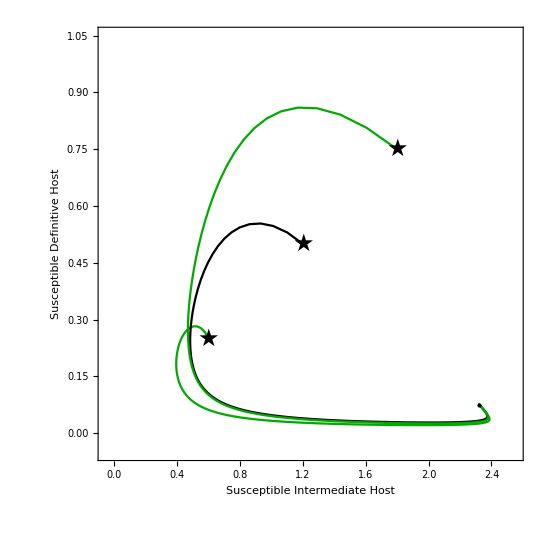

```mathematica
epilogHost1 = {{PointSize[Large],Point[Partition[Riffle[ieq1,deq1],2]]}, Table[{Black, Text[Style[★, FontSize->24], {ics⟦i,1,2⟧, ics⟦i,4,2⟧}, {0, 0}]},{i,1,Length[ics],1}] };
ppHost1=ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsolNL⟦1⟧],Evaluate[{Is[t], Ds[t]}/.ndsolNL⟦2⟧],Evaluate[{Is[t], Ds[t]}/.ndsolNL⟦3⟧]}, {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->{Darker[Green],Black,Darker[Green]}, FrameStyle -> frameStyle, PlotRange->range1, FrameLabel->{"Susceptible Intermediate Host", "Susceptible Definitive Host"}, LabelStyle->labelStyle,   ImageSize->imageSize/1.1, Epilog->epilogHost1]
```

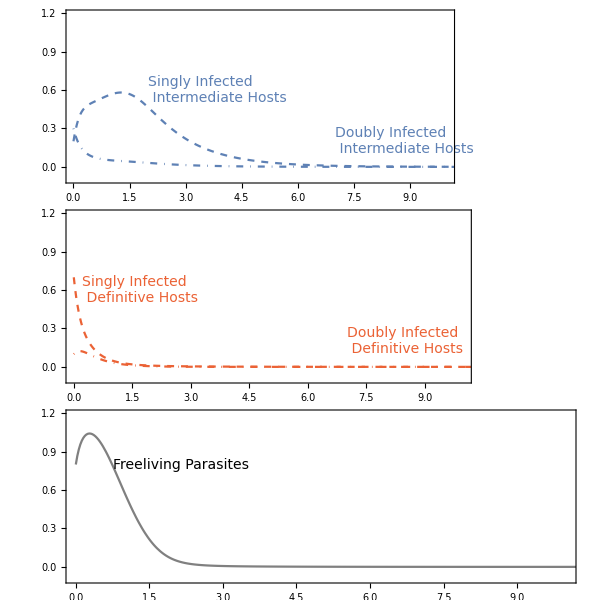

```mathematica
ppParasite1
```

## Disease stable equilibrium

```mathematica
(*Set parameters*)prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.05, fw -> 45, fww-> 45,δ-> 0.9, k -> 0.26, h-> 0.6};
condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};
maxt =80;

(*Set range for the plot and initial values*)
range2 = Full;
inits = {{Is[0]==0.9,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.9,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472},{Is[0]==0.4588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472},{Is[0]==1.45,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==1.2,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472}};
(*Solving the ode for different initial values*)
ndsolDS = Table[NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, inits⟦i⟧], varRes, {t, 0, maxt}],{i,1,Length[inits],1} ];

(*Get the dynamics of initial condition 2*)
ieq2 = Evaluate[Is[maxt]/.ndsolDS][[1]];
deq2 = Evaluate[Ds[maxt]/.ndsolDS][[1]];

(*Annotation for different lines*)epilogParas21 = {{ihostCol, Text[Style["Singly Infected \n Intermediate Hosts", FontSize->14], {30, -1.}, {-1.05, 0}]}, {ihostCol, Text[Style["Doubly Infected \n Intermediate Hosts", FontSize->14], {30, -4.2}, {-1.05, 0}]}};
epilogParas22 = {{dhostCol, Text[Style["Singly Infected \n Definitive Hosts", FontSize->14], {30, -4.1}, {-1.05, 0}]},{dhostCol, Text[Style["Doubly Infected \n Definitive Hosts", FontSize->14], {30, -7.5}, {-1.05, 0}]}};
epilogParas23 = {{Black, Text[Style["Freeliving Parasites", FontSize->14], {30, -3.2}, {-1.08, 0}]}};
trajectStyle = {{Gray, Thick}};
spcl=ndsolDS⟦2⟧;

(*Plot trajectories of infected intermediate hosts, definitive hosts, and free-living parasite with respect to time*)ppParasite21 =LogPlot[Evaluate[{Iw[t], Iww[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->{{ihostCol, Dashed}, {ihostCol, DotDashed}},PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle, ImageSize->imageSize, Epilog->epilogParas21] ;
ppParasite22 =LogPlot[Evaluate[{Dw[t], Dww[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->{{dhostCol, Dashed}, {dhostCol, DotDashed}},PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle,  ImageSize->imageSize, Epilog->epilogParas22] ;
ppParasite23 =LogPlot[Evaluate[{ W[t]}/.spcl], {t, 0, maxt}, AspectRatio->1/3, PlotStyle->trajectStyle,PlotRange-> All, Frame-> includeFrame, FrameStyle->frameStyle, ImageSize->imageSize, Epilog->epilogParas23] ;


ppParasite2 = GraphicsColumn[{ppParasite21, ppParasite22, ppParasite23}, Spacings-> 0, ImageSize->{600, 600}];
```

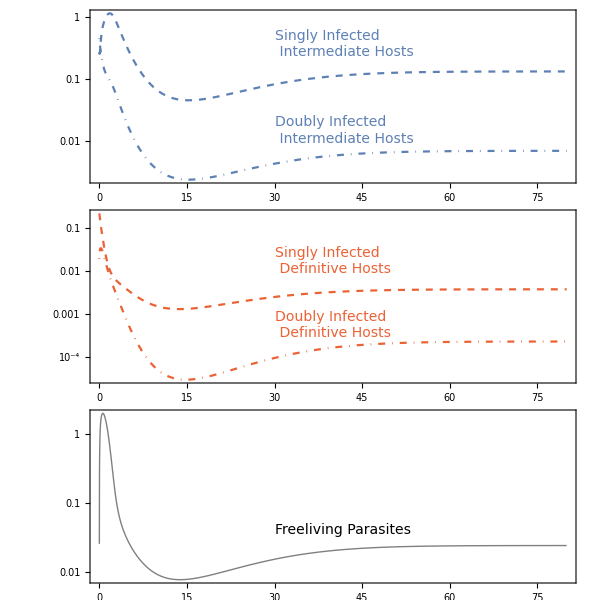

```mathematica
ppParasite2
```

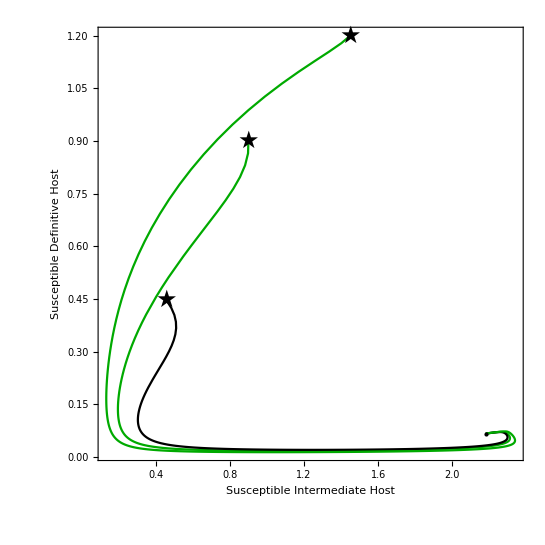

```mathematica
(*Plot phase plane of susceptible intermediate and definitive hosts*)epilogHost2 = {{PointSize[Large],Point[Partition[Riffle[ieq2,deq2],2]]}, Table[{Black, Text[Style[★, FontSize->24], {inits⟦i,1,2⟧, inits⟦i,4,2⟧}, {0, 0}]},{i,1,Length[inits],1}] };
ppHost2=ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsolDS⟦1⟧],Evaluate[{Is[t], Ds[t]}/.ndsolDS⟦2⟧],Evaluate[{Is[t], Ds[t]}/.ndsolDS⟦3⟧]}, {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->{Darker[Green],Black,Darker[Green]}, FrameStyle -> frameStyle, PlotRange->range2, FrameLabel->{"Susceptible Intermediate Host", "Susceptible Definitive Host"}, LabelStyle->labelStyle,   ImageSize->imageSize/1.1, Epilog->epilogHost2]
```

## Combined disease free and disease stable ecology plot (Figure 3)

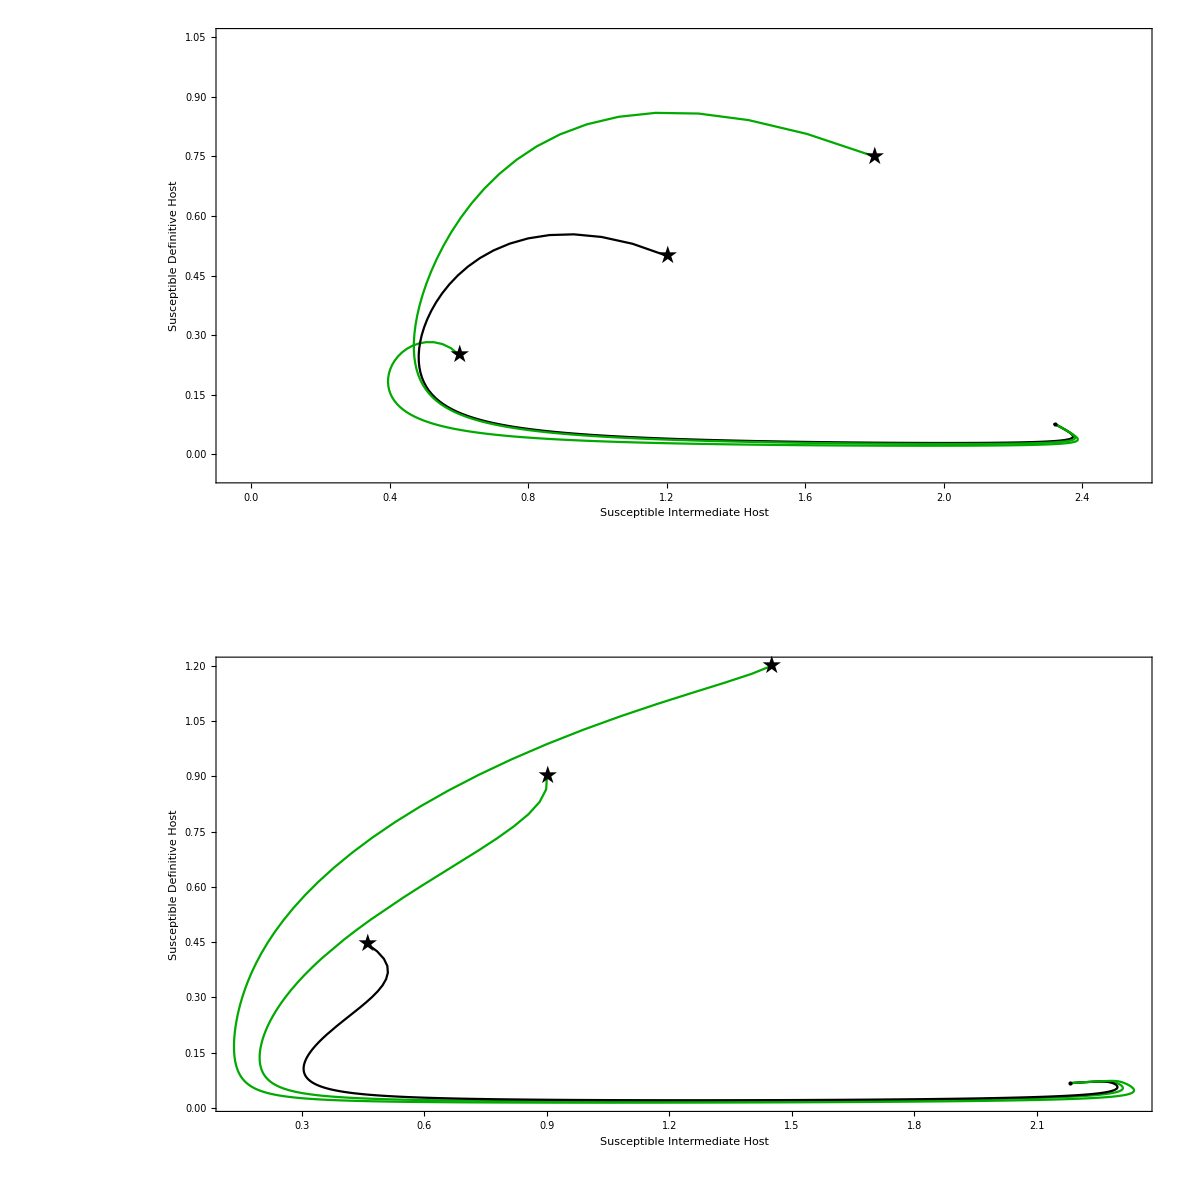

```mathematica
epilogAxesCombiPanel = {Text[Style["A)", Black, 24], {100, -10}], Text[Style["Time", Black, 24], {330, -520}],Rotate[Text[Style["Density", Black, 24], {100, -240}], 90 Degree], Text[Style["B)", Black, 24], {660, -10}],Text[Style["C)", Black, 24], {100, -590}], Text[Style["Time", Black, 24], {330, -1120}], Rotate[Text[Style["Density", Black, 24], {100, -840}], 90 Degree],  Text[Style["D)", Black, 24], {660, -590}]};
GraphicsGrid[{{ppParasite1, ppHost1}, {ppParasite2, ppHost2}}, ImageSize->{1200, 1200}, Spacings->0, Epilog->epilogAxesCombiPanel]
(*Export["ecotraject_nonlinear.pdf", %, ImageResolution-> figResolution]*)
```

## Bifurcation for reproduction in single infection f_w (f_ww = ϵ f_w) (Figure 5)

```mathematica
fwstart = 33;
fwend = 45;
fwstep = 0.1;
fwrange = Range[fwstart, fwend, fwstep];
```

## Parameter set 1 (bistability) Figure 5 Panel B-C

CALCULATE BIFURCATION

```mathematica
parfw1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4, h-> 0.6};
(*Find all solutions of the system with the given parameter values*)
solsfwAll1 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw1/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
fwAllPositive1= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw1, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
(*Select disease free solutions*)
solsfwzero1 = Select[solsfwAll1, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

CALCULATE DYNAMICS

```mathematica
maxt1 = 300;
init1 = {Is[0]==0.1588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472};
solsbistable1 = NDSolve[Join[sysNDSolvefunc1/.fww -> ϵ fw /.parfw1/.fw-> 39/.ϵ -> 4, init1], varRes, {t, 0, maxt1}] ;
maxt2 = 300;
init2 = {Is[0]==1.1588921303535818,Iw[0]==0.27287415391003156,Iww[0]==0.46321506893225517,Ds[0]==0.4460456255182149,Dw[0]==0.214956687585793,Dww[0]==0.018729116483236274,W[0]==0.025702772691754472};
solsbistable2 = NDSolve[Join[sysNDSolvefunc1/.fww -> ϵ fw /.parfw1/.fw-> 39/.ϵ -> 4, init2], varRes, {t, 0, maxt2}] ;
```

PLOT

RGBColor[0.701961, 0.890196, 0.933333]

RGBColor[0.501961, 0.709804, 0.835294]

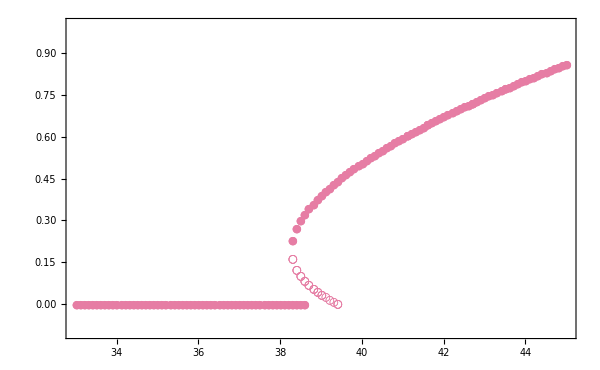

reproduction_bifurcationB.pdf

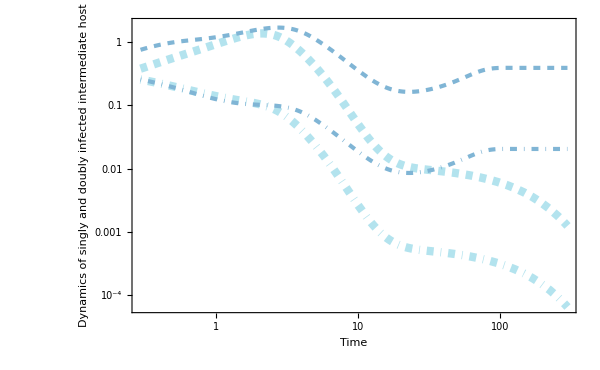

reproduction_bifurcationD.pdf

```mathematica
fwlist = fw/.Flatten[fwAllPositive1, 1];
eqfwlist = eq/.Flatten[fwAllPositive1, 1];
eqfwzero = ConstantArray[solsfwzero1, Length[fwrange]];
col1 = ColorData["GeologicAges", "ColorList"][[45]];
colLine1 = ColorData["GeologicAges", "ColorList"][[27]]
colLine2 = ColorData["GeologicAges", "ColorList"][[25]]
thickness = 0.005;
rangeIw = {{fwstart, fwend}, {-0.1, 1.}};

Iwfwlist = Iw/.eqfwlist;

sdat1 = MakeListPlotData[fwlist, Iwfwlist];
markers1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw1, fw, fwlist, eqfwlist, { "✶","○", "●" }];

zdat1 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw1, fw, fwrange, eqfwzero, { "✶","○", "●" }];

pIw = ListPlot[Join[sdat1, zdat1], PlotMarkers->Join[markers1, markerz1], PlotStyle->col1, PlotRange->rangeIw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" Reproduction in single infection (f_w)", "Equilibrium of density of \n singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle]
Export["reproduction_bifurcationB.pdf", %, ImageResolution-> figResolution]

parfw1Dynamics = LogLogPlot[{Evaluate[Iw[t]]/.solsbistable1, Evaluate[Iww[t]]/.solsbistable1, Evaluate[Iw[t]]/.solsbistable2, Evaluate[Iww[t]]/.solsbistable2},{t, 0, maxt1},PlotStyle->{{colLine1, Dashed, Thickness[thickness*2]}, {colLine1, DotDashed, Thickness[thickness * 2]}, {colLine2, Dashed, Thickness[thickness]}, {colLine2, DotDashed, Thickness[thickness]}}, PlotRange-> {{0, maxt1}, {-0.1, 1.9}}, Frame-> includeFrame, FrameStyle->frameStyle,LabelStyle->labelStyle, ImageSize->imageSize, FrameTicksStyle->Directive[Black,20],FrameLabel->{"Time", "Dynamics of singly and doubly \n infected intermediate host"}]
Export["reproduction_bifurcationD.pdf", %, ImageResolution-> figResolution]
```

## Parameter set 2 (single equilibrium) Figure 5 Panel B

CALCULATION

```mathematica
parfw2 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 1, h-> 0.6};
(*Find all solutions of the system with the given parameter values*)
solsfwAll2 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw2/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw2= Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero2 = Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

(*Select disease circulation solutions*)
fwAllPositive2= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw2, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
```

Part::partw: Part 1 of {} does not exist.

PLOTTING

```mathematica
rangeIw = {{fwstart, fwend}, {-0.01, 0.2}};
fwlist = fw/.Flatten[fwAllPositive2, 1];
eqfwlist = eq/.Flatten[fwAllPositive2, 1];
eqfwzero = ConstantArray[solsfwzero2, Length[fwrange]];
col2 = ColorData["GeologicAges", "ColorList"][[35]];

Iwfwlist = Iw/.eqfwlist;

sdat3 = MakeListPlotData[fwlist, Iwfwlist];
markers3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw2, fw, fwlist, eqfwlist, { "✶","○", "●" }];
zdat3 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw2, fw, fwrange, eqfwzero, { "✶","○", "●" }];

ppIw = ListPlot[Join[sdat3, zdat3], PlotMarkers->Join[markers3, markerz3], PlotStyle->col2 , PlotRange->rangeIw, Frame->includeFrame, ImageSize->imageSize,FrameLabel->{"Reproduction in single infection (f_w)", "Equilibrium of density of \n singly infected intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle(*, PlotLabel->Pane["B) f_ww = f_w", Alignment->Left, ImageSize->panellabel]*)];
Export["reproduction_bifurcationC.pdf", %, ImageResolution-> figResolution]
```

reproduction_bifurcationC.pdf

## Bifurcation ϵ and f_w (f_ww = ϵ f_w) Figure 5 Panel A

CALCULATE

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, h-> 0.6};
ϵstart = 0;
ϵend = 6;
ϵinterval = 0.025;
fwstart = 33;
fwend =45;
fwinterval = 0.25;

ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {fw -> i}, {ϵ-> j}, ϵfw, eq,varRes,12],{i, fwstart, fwend, fwinterval}, {j, ϵstart, ϵend, ϵinterval}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859504757407689. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.859451508977895. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

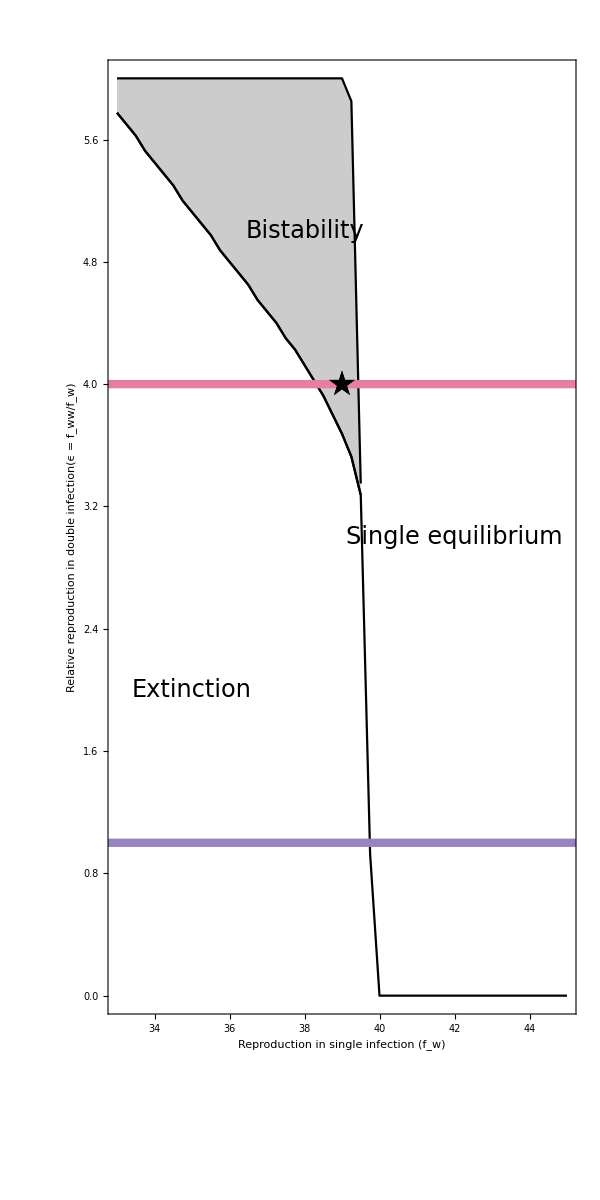

reproduction_bifurcationA.pdf

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 2];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 2];
rangeϵfw= { {fwstart , fwend}, {ϵstart , ϵend}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist, eqϵfw, colorstable, True];
MakeListPlotData[ϵfwlist[[All, 1]], ϵfwlist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> Directive[Thick,
Red], LabelStyle->labelStyle,FrameStyle->frameStyle,AspectRatio->1];
GetBoundaryLineBiStable[ϵfwlist];
p1 =ListLinePlot[%, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Reproduction in single infection (f_w)", "Relative reproduction in double infection(ϵ = f_ww/f_w)"}, LabelStyle->labelStyle,GridLines->{{},{{1, col2}, {4, col1}}},GridLinesStyle->Thickness[0.01], PlotStyle-> Black, Filling-> {1-> {2}}];
GetBoundaryLineSingle[ϵfwlist];
p2 = ListLinePlot[%,  PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black];
ip = ip = ListLinePlot[{{39, 4}}, PlotRange->rangeϵfw, PlotMarkers -> {"★", 28},Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black, ImageSize->imageSize, LabelStyle->labelStyle];
GraphicsGrid[{{p0, Show[{p1, p2}]}}];
pϵfw = Show[{p1, p2, ip}, ImageSize-> {imageSize , imageSize * 2},Epilog->{ Text[Style["Extinction", FontSize->24], {35, 2}],
			Text[Style["Single equilibrium", FontSize->24], {42, 3}], Text[Style["Bistability", FontSize->24], {38, 5.}]}, AspectRatio-> 2/1, LabelStyle->labelStyle, ImagePadding->{{90(*left*),5(*right*)},{65(*bottom*),10(*top*)}}]
Export["reproduction_bifurcationA.pdf", %, ImageResolution-> figResolution]
```

## Contour plot (Figure 4)

Calculate

```mathematica
βwstart = 0;
βwend = 4;
βwstep =0.15;
βwwstart = 0;
βwwend =4;
βwwstep = 0.15;
range= {{βwstart, βwend}, {βwwstart, βwwend}};
parmanipR0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26, ϵ-> 4.5, fw -> 37, h-> 0.6};
		    
manipAllResultsR0 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipR0, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

Plot

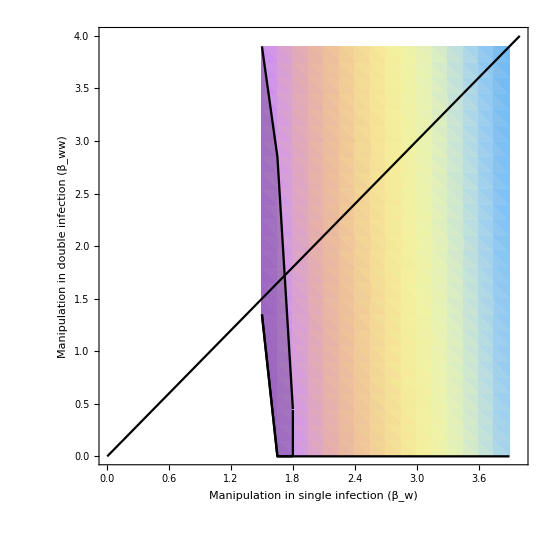

manip_bifur_R0.pdf

```mathematica
thickR0 = 0.003;
equilibrium =eq/. Flatten[manipAllResultsR0 , 2];
parslist = β/.Flatten[manipAllResultsR0, 2];
R0numeric = R0func1/.{Iw -> 0, Iww->0, Dw-> 0, Dww->0 , W-> 0}/.diseasefree/.fww-> ϵ fw/.parmanipR0/. Thread[{Thread[βw->parslist[[All, 1]]],Thread[βww-> parslist[[All, 2]]]}];

zrange={Min[R0numeric], Max[R0numeric]};
barleg=BarLegend[{coldat, zrange}, {1, 1.1, 1.2, 1.3, 1.4}, LegendMarkerSize->320, LegendLayout->"Row"];
(* Plot R0*)
Join[parslist, Partition[R0numeric, 1], 2];
R0g = ListDensityPlot[%,  Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection (β_w)", "Manipulation in double infection (β_ww)"}, ImageSize->imageSize, ColorFunction->coldat,PlotLegends->Placed[barleg, {Above,Right}](*, ColorFunctionScaling->False*),PlotRange->range, ImagePadding->{{60,5},{65,30}}];
(* Plot Subscript[β, w] = Subscript[β, ww] line*)
p0 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black, ImageSize->imageSize];

(* Plot bistability area*)
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipR0,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
bnd1 = GetBoundaryLineBiStable[parslist];
p1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection (β_w)", "Manipulation in double infection (β_ww)"}, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thickR0], Black},{Thickness[thickR0],Black}}, Filling-> {{1-> {2}}},FillingStyle->Directive[Black,HatchFilling[Pi, 2, 6]] ,ImageSize->imageSize];
bnd2 = GetBoundaryLineSingle[parslist];
p2= ListLinePlot[Join[{%, {{1.55, 4.6}, {1.55, 6}}, {{1.8, 0}, {1.8, 0.44}}}],  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> { {Thickness[thickR0], Black},{Thickness[thickR0],  Black}}];
p3 = Show[{p1,p2, p0}];

R0gfinal = Show[{  R0g, p3}, ImageSize-> 550]
Export[ "manip_bifur_R0.pdf", %, ImageResolution-> figResolution]
```

## Manipulation ratio representation

```mathematica
βwwstart = 0.1;
βwwend = 3;
βwwstep =0.03;
ϵstart = 0.5;
ϵend = 12;
ϵstep = 0.2;
alpha = 0.6;
```

### Changing reproduction in single infection

### fw = 37, βw = 1.65 (Figure 6 Panel D)

CALCULATION

```mathematica
(*Set parameters*)parmanipβϵ ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 37, h-> 0.6, βw-> 1.65};
range1= {{βwwstart/(βw/.parmanipβϵ),βwwend/(βw/.parmanipβϵ) }, {ϵstart, ϵend + 0.1}}
```

{{0.0606061,1.81818},{0.5,12.1}}

```mathematica
(*Bifurcation value*)manipβϵAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

PLOT

```mathematica
equilibrium =eq/. Flatten[manipβϵAllResults, 2];
parslist = βϵ/.Flatten[manipβϵAllResults, 2];

(*Create markers for equilibrium*)
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ), parslist[[All, 2]]];
(*Plot equilibrium as points with blue as stable points and orange as unstable points*)pβϵ = ListPlot[%,  PlotStyle->marklist, PlotRange->range1, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
(*Connect points at boundary*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
(*Draw upper boundary*)lpβϵ1 =ListLinePlot[%,  PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle,PlotStyle-> {{Thick, Thickness[thick],colbifur[[3]]}, {Thick, Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {{2}, Directive[Opacity[alpha],colbifurfilling[[3]]]}},  ImageSize->imageSize];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ, 1}, Length@GetBoundaryLineSingle[parslist]];
(*Draw lower boundary*)lpβϵ2= ListLinePlot[%, PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thick,Thickness[thick], colbifur[[3]]},FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", "Relative reproduction \n in double infections(f_ww/f_w)"}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ = Show[{lpβϵ2,lpβϵ1}];
GraphicsGrid[{{pβϵ, lβϵ}}]
```

-Graphics-

### fw = 38, βw = 1.65 (Figure 6 Panel B)

```mathematica
(*Set parameters*)parmanipβϵ1 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.65};
(*Equilibrium values*)manipβϵ1AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ1, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ1AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ1AllResults, 2];

(*Mark equilibrium as stable and unstable*)marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ1,{βww, ϵ}, parslist, equilibrium, colorstable, True];
(*Plot unstable and stable equilibrium*)
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ1), parslist[[All, 2]]];
pβϵ1= ListPlot[%,  PlotStyle->marklist, PlotRange->range1, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*Connect boundary points*)
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
(*Upper boundary*)lpβϵ1 =ListLinePlot[%,  PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " \n "},PlotStyle-> {{Thick, Thickness[thick],colbifur[[3]]}, {Thick, Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {{2}, Directive[Opacity[alpha], colbifurfilling[[3]]]}},  ImageSize->imageSize];
(*Lower boundary*)
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ1, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range1, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thick,Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ1 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ1, lβϵ1}}]
```

-Graphics-

### fw = 37, βw = 1.60 (Figure 6 Panel C)

```mathematica
(*Set parameters*)parmanipβϵ2 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 37., h-> 0.6, βw-> 1.60};
(*Calculate equilibrium*)manipβϵ2AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ2, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
range2= {{βwwstart/(βw/.parmanipβϵ2),βwwend/(βw/.parmanipβϵ2) }, {ϵstart, ϵend + 0.1}};
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ2AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ2AllResults, 2];

(*Mark stable and unstable equilibrium *)
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ2,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ2), parslist[[All, 2]]];
(*Plot stable and unstable equilibrium*)pβϵ2= ListPlot[%,  PlotStyle->marklist, PlotRange->range1, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];
(*Connect boundary points*)
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];

(*Upper boundary*)lpβϵ1 =ListLinePlot[%,  PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " Relative reproduction \n in double infections(f_ww/f_w) "},PlotStyle-> {{Thickness[thick],colbifur[[3]]}, {Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[3]]],  ImageSize->imageSize];
(*Lower boundary*)
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ2, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray, HatchFilling[]]];
lβϵ2 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ2, lβϵ2}}]
```

-Graphics-

### fw = 38, βw = 1.60 (Figure 6 Panel A)

```mathematica
(*Set parameters*)parmanipβϵ3 ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.60};
(*Calculate equilibrium*)manipβϵ3AllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβϵ3, {βww-> x}, {ϵ-> y}, βϵ, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, ϵstart, ϵend, ϵstep}];
```

```mathematica
equilibrium =eq/. Flatten[manipβϵ3AllResults, 2];
parslist = βϵ/.Flatten[manipβϵ3AllResults, 2];

(*Mark stable and unstable equilibrium*)marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβϵ3,{βww, ϵ}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβϵ3), parslist[[All, 2]]];
pβϵ3= ListPlot[%,  PlotStyle->marklist, PlotRange->range2, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "f_ww/f_w"}, LabelStyle->labelStyle];

(*Connect boundary points*)
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
(*Upper boundary*)lpβϵ1 =ListLinePlot[%,  PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infections (β_ww/β_w)", " \n "},PlotStyle-> {{Thickness[thick],colbifur[[3]]}, {Thickness[thick],colbifur[[3]]}}, Filling-> {1-> {2}},FillingStyle->Directive[Opacity[alpha], colbifurfilling[[3]]],  ImageSize->imageSize];
(*Lower boundary*)
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβϵ3, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβϵ2= ListLinePlot[%, PlotRange->range2, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[3]]}, Filling->Bottom, FillingStyle->Directive[LightGray,HatchFilling[]]];
lβϵ3 = Show[{lpβϵ1,lpβϵ2}];
GraphicsGrid[{{pβϵ3, lβϵ3}}]
```

-Graphics-

### Combined graph (Figure 6)

```mathematica
line = {Graphics[{Thickness[0.005],Black,Line[{{1, range[[2]][[1]]}, {1, 12.5}}]}], Graphics[{Thickness[0.005],Black,Line[{{range[[1]][[1]], 1}, {2.25, 1}}]}]};
arrowsize = {-0.02,0.02}
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range1[[1]][[1]], 12.4}}], Text[Style["Sabotage", FontSize->22], {0.5, 12.9}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range1[[1]][[2]], 12.4}}], Text[Style["Cooperation", FontSize->22], {1.4, 12.9}]} ];
arrow3 = Graphics[{Arrowheads[arrowsize],Arrow[{{1.9, 1}, {1.9, range1[[2]][[2]]}}], Rotate[Text[Style["Enhancement", FontSize->22], {1.96, 6.7}], -90 Degree]} ];
arrow4 = Graphics[{Text[Style["Suppression", FontSize->22], {2.01, 0.55}]} ];
plotlβϵfull1 = Show[{ lβϵ, line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{150, 200}, {100, 45}},
	 Epilog->{ Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationA.pdf", %, ImageResolution-> figResolution]
plotlβϵfull1 = Show[{ lβϵ1,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 200}, {100, 45}},
	 Epilog->{ Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationB.pdf", %, ImageResolution-> figResolution]

arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range2[[1]][[1]], 12.4}}], Text[Style["Sabotage", FontSize->22], {0.5, 12.9}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1, 12.4}, {range2[[1]][[2]], 12.4}}], Text[Style["Cooperation", FontSize->22], {1.4, 12.9}]} ];
arrow3 = Graphics[{Arrowheads[arrowsize],Arrow[{{1.96, 1}, {1.96, range2[[2]][[2]]}}], Rotate[Text[Style["Enhancement", FontSize->22], {2.02, 6.7}], -90 Degree]} ];
arrow4 = Graphics[{Text[Style["Suppression", FontSize->22], {2.07, 0.55}]} ];
plotlβϵfull1 = Show[{ lβϵ2,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{150, 200}, {100, 45}},
	 Epilog->{ Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.7, 11.2}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationC.pdf", %, ImageResolution-> figResolution]
plotlβϵfull1 = Show[{ lβϵ3,line, arrow1, arrow2, arrow3, arrow4},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 200}, {100, 45}},
	 Epilog->{ Text[Style["Extinction", FontSize->24], {0.3, 2.}],Text[Style["Single \n equilibrium", FontSize->24], {1.6, 9.5}]}, ImageSize-> {1000,650}]
Export["ratio_reproduction_manipulationD.pdf", %, ImageResolution-> figResolution]
```

{-0.02,0.02}

-Graphics-

ratio_reproduction_manipulationA.pdf

-Graphics-

ratio_reproduction_manipulationB.pdf

-Graphics-

ratio_reproduction_manipulationC.pdf

-Graphics-

ratio_reproduction_manipulationD.pdf

## Changing p (Figure 7 Panel A)

```mathematica
βwwstart = 0.1;
βwwend = 6.8;
βwwstep = 0.05;
coldat="Rainbow";
```

0.05

CALCULATION

```mathematica
parmanipβp ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.05, δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.4, ϵ -> 4.5};
manipβpAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβp, {βww-> x}, {p-> y}, βp, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, 0, 1,0.007}];
```

PLOT

```mathematica
equilibrium =eq/. Flatten[manipβpAllResults, 2];
parslist = βp/.Flatten[manipβpAllResults, 2];
range= {{βwwstart/(βw/.parmanipβp),βwwend/(βw/.parmanipβp) }, {0, 1}};
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβp,{βww, p}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβp), parslist[[All, 2]]];
pβp = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "p"}, LabelStyle->labelStyle];
(*MapThread to get ratio as xaxis*)
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Relative manipulation in double infection (β_ww/β_w)", "Cotransmission (p) \n parasite pool - intermediate host"},PlotStyle-> {{ Thickness[thick],Black}, {Thickness[thick],Black}}, Filling-> {1-> {2}},FillingStyle->colbifurfilling[[3]],  ImageSize->imageSize,PlotLabel->Pane["A)", Alignment->Left, ImageSize->panellabel], InterpolationOrder->intorder];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβp, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], Black}, InterpolationOrder->intorder, Filling->Bottom, FillingStyle->Directive[LightGray, HatchFilling[]]];
line = {Graphics[{Thickness[0.005],Black,Line[{{1, 0}, {1, 1.1}}]}]};
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, { βwwstart/(βw/.parmanipβp),1.02}}], Text[Style["Sabotage", FontSize->20], {0.5, 1.08}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, {βwwend/(βw/.parmanipβp), 1.02}}], Text[Style["Cooperation", FontSize->20], {2.9, 1.08}]} ];
lv = ListLinePlot[{{{0.,1},{0.8,1}}},PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], Black}, Filling-> Bottom, FillingStyle->Directive[LightGray, HatchFilling[]]];
lβp = Show[{ lpβp1,lpβp2, line,lv,  arrow1, arrow2},Epilog->{Text[Style["Extinction", FontSize->20], {0.5, 0.07}],Text[Style["Single \n equilibrium", FontSize->20], {3.3, 0.6}]},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 20}, {100, 45}}, ImageSize-> imageSize/1.5];
GraphicsGrid[{{pβp, lβp}}];
```

```mathematica
lβp
```

-Graphics-

## Changing q (Figure 7 Panel B)

CALCULATION

```mathematica
parmanipβq ={ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.05, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,δ-> 0.9, k -> 0.26,  fw -> 38, h-> 0.6, βw-> 1.45, ϵ -> 4.5};
manipβqAllResults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipβq, {βww-> x}, {q-> y}, βq, eq,varRes, 15],{x, βwwstart, βwwend, βwwstep}, {y, 0, 1, 0.007}];
```

PLOT

```mathematica
equilibrium =eq/. Flatten[manipβqAllResults, 2];
parslist = βq/.Flatten[manipβqAllResults, 2];
range= {{βwwstart/(βw/.parmanipβq),βwwend/(βw/.parmanipβq) }, {0, 1}};
arrowsize = {-0.02,0.02};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipβq,{βww, q}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]]/(βw/.parmanipβq), parslist[[All, 2]]];
pβq = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"β_ww/β_w", "q"}, LabelStyle->labelStyle];
Join[Thread@{parslist[[All, 1]]/(βw/.parmanipβq), parslist[[All, 2]]},Idensity, 2];
MapThread[#1/#2&, {GetBoundaryLineBiStable[parslist],{ ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineBiStable[parslist][[1, All]]], ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineBiStable[parslist][[2, All]]]}}];
lpβq1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"β_ww/β_w", "Cotransmission (q) \n intermediate - definitive host"},PlotStyle-> {{Thickness[thick],Black}, {Thickness[thick],Black}}, Filling-> {1-> {2}},FillingStyle->colbifurfilling[[3]],  ImageSize->imageSize, PlotLabel->Pane["B)", Alignment->Left, ImageSize->panellabel], InterpolationOrder->intorder];
GetBoundaryLineSingle[parslist]/ConstantArray[{βw/.parmanipβq, 1}, Length@GetBoundaryLineSingle[parslist]];
lpβq2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick],Black}, InterpolationOrder->intorder,Filling-> Bottom, FillingStyle->Directive[LightGray, HatchFilling[]]];
line = {Graphics[{Thickness[0.005],Black,Line[{{1, 0}, {1, 1.1}}]}]};
arrow1 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, { βwwstart/(βw/.parmanipβp),1.02}}], Text[Style["Sabotage", FontSize->20], {0.5, 1.08}]}];
arrow2 = Graphics[{Arrowheads[arrowsize],Arrow[{{1., 1.02}, {βwwend/(βw/.parmanipβp)-0.1, 1.02}}], Text[Style["Cooperation", FontSize->20], {2.9, 1.08}]} ];
arrow3 = Graphics[{Arrow[{{0.2, -0.06}, {0.2, 0.08}}]}];
lβq = Show[{lpβq1,lpβq2, line, arrow1, arrow2, arrow3}, Epilog-> {Text[Style["Extinction", FontSize->20], {0.2, -0.09}],Text[Style["Single \n equilibrium", FontSize->20], {3.3, 0.6}]},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding-> {{110, 20}, {110, 45}}, ImageSize-> imageSize/1.5]
(*GraphicsGrid[{{pβq, lβq}}]*)
```

{-0.02,0.02}

Join::headsd: Expression Idensity at position 2 is expected to have head List for all expressions at level 2.

-Graphics-

## Combined graph

```mathematica
GraphicsGrid[{{lβp, lβq}},ImageSize->imageSize*2.8, Spacings-> -60]
Export["coinfect_transmission.pdf", %, ImageResolution-> figResolution]
```

-Graphics-